{0.0401195,{x→0.5}}

{0.000111654,{x→0.753617}}

{0.000148803,{x→1.25068}}

{0.000162148,{x→1.74965}}

{1.,{x→1.5708}}

0.000114807

2.5473×10^-9

4.40677×10^-9

5.39603×10^-9

1.1892

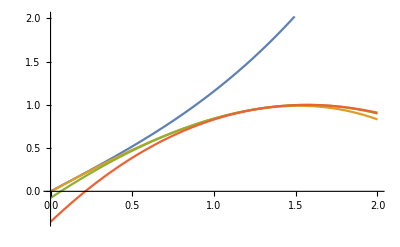

```mathematica
var1 = {(0.160478),(-0.00205866),(1),(0)};
var2 = {(-0.121188),(-0.064608),(1.03308),(-0.00581466)};
var3 = {(-0.052226),(-0.273718),(1.24442),(-0.0770009)};
var4 = {(0.0295224),(-0.641877),(1.79709),(-0.353557)};
f[t_]:= Sin[t]
a[t_] := (var1[[1]])*t^3+(var1[[2]])*t^2+(var1[[3]])*t+(var1[[4]])
b[t_] := (var2[[1]])*t^3+(var2[[2]])*t^2+(var2[[3]])*t+(var2[[4]])
c[t_] := (var3[[1]])*t^3+(var3[[2]])*t^2+(var3[[3]])*t+(var3[[4]])
d[t_] := (var4[[1]])*t^3+(var4[[2]])*t^2+(var4[[3]])*t+(var4[[4]])
NMaximize[{Abs[f[x]-a[x]], 0<=x<=0.5}, x]
NMaximize[{Abs[f[x]-b[x]], 0.5<=x<=1}, x]
NMaximize[{Abs[f[x]-c[x]], 1<=x<=1.5}, x]
NMaximize[{Abs[f[x]-d[x]], 1.5<=x<=2}, x]
NMaximize[{Abs[f''''[x]], 0<=x<=2}, x]
NIntegrate[Abs[(f[x]-a[x])^2],{x,0,0.5}]
NIntegrate[Abs[(f[x]-b[x])^2],{x,0.5,1}]
NIntegrate[Abs[(f[x]-c[x])^2],{x,1,1.5}]
NIntegrate[Abs[(f[x]-d[x])^2],{x,1.5,2}]
NIntegrate[Abs[f''''[x]]^2, {x,0,2}]

Plot[{a[x],b[x],c[x], d[x]},{x,0,2 }]
```

```mathematica
FullForm[∞]
```

DirectedInfinity[1]

```mathematica
N[(-161280+80640 π-94080 π^2+67200 π^3+343422 π^4+45149 π^5+1611 π^6)/(840 π^3)]
```

1922.22

```mathematica
N[1/560 (761752-23730 Cos[2]-355740 Cos[4]+87185 Sin[2]-170345 Sin[4])]
```

2164.91

```mathematica
N[(18936008-2553912 Cos[1]-666222 Cos[2]+1747512 Cos[3]+15472436 Cos[4]-8886832 Sin[1]+2540475 Sin[2]+5116912 Sin[3]-2554963 Sin[4])/1680]
```

2070.01

```mathematica
N[1/560 (232552+23730 Cos[2]-87185 Sin[2])]
```

256.071

```mathematica
N[(1709096-1080504 Cos[1]-6551682 Cos[2]+4373304 Cos[3]-40 Cos[4]-9125936 Sin[1]+9071685 Sin[2]-651664 Sin[3]-96 Sin[4])/1680]
```

0.00371097

```mathematica
N[1/168 (16300+23390 Cos[10]-40320 Sin[5]+25991 Sin[10])]
```

126.18

```mathematica
N[1/24 (36140-6750 Cos[10]-5811 Sin[10])]
```

1873.54

```mathematica
N[1/168 (16300+23390 Cos[10]-40320 Sin[5]+25991 Sin[10])]
```

126.18

```mathematica
N[1/24 (36140+6750 Cos[10]+5811 Sin[10])]
```

1138.12

```mathematica
N[1/168 (80104+19326 Cos[10]-89363 Sin[10])]
```

669.663

```mathematica
N[1/24 (36140+6750 Cos[10]+5811 Sin[10])]
```

1138.12

```mathematica
∫5 Abs[-8 t Cos[t]-12 Sin[t]+t^2 Sin[t]]^2 ⅆt
```

5 ∫Abs[-8 t Cos[t]-12 Sin[t]+t^2 Sin[t]]^2 ⅆt

```mathematica
N[1/168 (80104+19326 Cos[10]-89363 Sin[10])]
```

669.663

```mathematica
N[(3 (-2240+23 π^4))/(140 π^3)]
```

0.000282726

```mathematica
N[(-6720+3360 π-840 π^2+280 π^3+69 π^4)/(140 π^3)]
```

2.52213

```mathematica
N[(3 (-2240+23 π^4))/(140 π^3)]
```

0.000282726

```mathematica
N[π/2]
```

1.5708

```mathematica
N[(-161280+80640 π-13440 π^2+366 π^4+13 π^5+π^6)/(840 π^3)]
```

0.0000737504

```mathematica
N[(161280-53760 π^2+10080 π^3+2046 π^4-631 π^5+57 π^6)/(840 π^3)]
```

0.162529

```mathematica
N[(-161280+322560 π+53760 π^2-147840 π^3+884046 π^4-376237 π^5+41301 π^6)/(840 π^3)]
```

287.316

```mathematica
N[(-645120+927360 π+114240 π^2-369600 π^3+1419699 π^4-589033 π^5+64194 π^6)/(3360 π^3)]
```

112.181

```mathematica
N[(-161280+322560 π+53760 π^2-147840 π^3+884046 π^4-376237 π^5+41301 π^6)/(840 π^3)]
```

287.316

```mathematica
N[(-161280+322560 π+53760 π^2-147840 π^3+887406 π^4-447637 π^5+58591 π^6)/(840 π^3)]
```

99.1783

```mathematica
N[(-161280+80640 π-13440 π^2+366 π^4+13 π^5+π^6)/(840 π^3)]
```

0.0000737504

```mathematica
NumberForm[0.00007375039271872087,16]
```

0.00007375039271872086